# Wavefunctions overlap for Li and Yb Calculation

### Setting parameters

```mathematica
(*importing Andrew's library. Make sure to put the bands.m fiel under any of the directory shown after running the command $Path.*)
<< Bands`

(*Set parameters*)
q=0; (*quasimomentum; in the range (-1,1)*)
n=0; (*number of band; from {0,1,2,3,4}*)
min=0;
max=20; (* integration range, in unit of lattice sites*)
```

## 1 Dimensional Case

### Visualizing wavefunctions of Li and Yb in the given potential

```mathematica
(*Define 1D wavefunction*)
Wavefunction[q_, n_, u_]:=MathieuPotentialWaveFunction[TranslateQuasimomentum[q, n], u/4, z];

(* Set the potentail depth for Yb*)
Subscript[U, Yb] = 100;  (*potential depth Yb sees, in units of recoil energy*)
Subscript[U, Li]=2.2/29 Subscript[U, Yb];  (*potential depth Li sees, in units of recoil energy*)

(*Ploting wavefunctions of Li and Yb*)
Plot[{Re[Wavefunction[q,n,Subscript[U, Yb]]], Im[Wavefunction[q,n,Subscript[U, Yb]]],Re[Wavefunction[q,n,Subscript[U, Li]]], Im[Wavefunction[q,n,Subscript[U, Li]]]}, {z, 0, 8}, PlotRange->{0,2.5}, PlotStyle->{{Orange,Solid}, {Orange,Dashed},{Blue,Solid}, {Blue,Dashed} }, AxesLabel->{ "lattice unit", "Ψ(x)"}, PlotLegends->{"Re[Yb]", "Im[Yb]", "Re[Li]", "Im[Li]"},PlotLabel->"Li & Yb wavefunctions"];

(*Plotting norm of Li and Yb*)
Plot[{Norm[Wavefunction[q,n,Subscript[U, Yb]]],Norm[Wavefunction[q,n,Subscript[U, Li]]]},{z,0,8}, PlotRange->All, PlotStyle->{{Orange,Solid},{Blue,Solid}}, AxesLabel->{"lattice unit", "|Ψ(x)|"},PlotLegends->{"Yb", "Li"},PlotLabel->"Li & Yb probability distribution"];

(*Ploting Subscript[Ψ, Yb] Subscript[Ψ, Li]*)
Plot[{Re[Wavefunction[q,n,Subscript[U, Yb]]*Conjugate[Wavefunction[q,n,Subscript[U, Li]]]],Im[Wavefunction[q,n,Subscript[U, Yb]]*Conjugate[Wavefunction[q,n,Subscript[U, Li]]]]},{z,0,8},PlotRange->All, PlotStyle->{Solid, Dashed},AxesLabel->{"lattice unit", "Ψ_YbΨ_Li^*"},PlotLegends->{"Re", "Im"}, PlotLabel->"Li & Yb overlap wavefunction"];

(*Ploting |Subscript[Ψ, Yb] Subscript[Ψ, Li]|*)
Plot[Norm[Wavefunction[q,n,Subscript[U, Yb]]*Conjugate[Wavefunction[q,n,Subscript[U, Li]]]],{z,0,8}, PlotRange->All, PlotLabel->"Norm of Li & Yb overlap wavefunction", AxesLabel->{"lattice unit", "|Ψ_YbΨ_Li^*|"}];
```

### Calculating overlap and maximum of the product wave function of Li and Yb

```mathematica
(**Defining function to calcualet inner product and overlap*)
InnerProduct[min_, max_, q_,n_,u1_, u2_]:=NIntegrate[Wavefunction[q, n, u1]*Conjugate[Wavefunction[q,n,u2]],{z, min, max},PrecisionGoal->8, WorkingPrecision->16];
Overlap[min_,max_, q_, n_, u_]:= Norm[InnerProduct[min,max,q,n,2.2/29 u,u]]^2/Norm[InnerProduct[min,max,q,n,2.2/29 u,2.2/29 u]]^2;
(*
(*Ploting potentials Li and Yb see with respect to Subscript[U, Yb]*)
Plot[{Subscript[U, Yb],2.2/29 Subscript[U, Yb]}, {Subscript[U, Yb],0,50},PlotRange->All, AxesLabel->{"U_Yb", "U/recoil energy"}, PlotLegends->{"Yb", "Li"}];
(*Ploting overlap of Li and Yb with respect to Subscript[U, Yb]*)
ListPlot[Table[{ Subscript[U, Yb],Overlap[min,max,q,n,Subscript[U, Yb]]},{Subscript[U, Yb], 0,50}], PlotRange->All, AxesLabel->{"U_Yb", "|∫Ψ_YbΨ_Li^*ⅆx|^2/|∫Ψ_LiΨ_Li^*ⅆx|^2"},PlotLabel->"Yb-Li overlap, "];
(*Ploting max of |Subscript[Ψ, Yb] Subscript[Ψ, Li]^*| withing one unit cell*)
ListPlot[Table[{Subscript[U, Yb],First[FindMaximum[{Norm[Wavefunction[q,n,Subscript[U, Yb]]*Conjugate[Wavefunction[q,n,2.2/29 Subscript[U, Yb]]]],0≤z≤ 1},{z,0}]]}, {Subscript[U, Yb],0,10,2}], PlotRange->All, AxesLabel->{ "U_Yb","max(|Ψ_YbΨ_Li^*|)"},PlotLabel->"max of |Ψ_YbΨ_Li^*| over one unit cell"];
*)
```

### Cross check: When potential is large, approximate using quadratic function

```mathematica
(*Oscilator ground state function of an atom as a function of atom's recoil energy*)
OscilatorGroundState[s_]:= (2^(1/2)π)^(1/4)s^(1/8)Exp[-(2^(1/2)π^2 s^(1/2))/2 x^2];(*where s is the potential energy in terms of recoil*)

(*Evaluate overlap and max when potentail depth is large*)
Subscript[u, Yb]=500;
Subscript[u, Li]=2.2/29 Subscript[u, Yb];
(*Plotting approximated Li and Yb wavefunction*)
Plot[{OscilatorGroundState[Subscript[u, Yb]],OscilatorGroundState[Subscript[u, Li]]},{x,-1,1},PlotRange->All,PlotStyle->{Orange,Blue},PlotLegends->{"Yb", "Li"},AxesLabel->{"lattice unit","ψ_0(x)"}];
(*
(*Evaluate the overlap at the given potential above*)
(Integrate[Norm[OscilatorGroundState[Subscript[u, Yb]]*Conjugate[OscilatorGroundState[Subscript[u, Li]]]],{x, -10,10}])^2;

(*Plotting |Subscript[Ψ, Yb] Subscript[Ψ, Li]^*|*)
Plot[Norm[OscilatorGroundState[Subscript[u, Yb]]*Conjugate[OscilatorGroundState[Subscript[u, Li]]]],{x,-1,1},PlotRange->All];

(*Find max of |Subscript[Ψ, Yb] Subscript[Ψ, Li]^*| within one unit cell at the given potential above*)
FindMaximum[Norm[OscilatorGroundState[Subscript[u, Yb]]*Conjugate[OscilatorGroundState[Subscript[u, Li]]]],{x,-1,1}];

(*Plotting the harmonic oscillator approx of Li-Yb overlap*)
ListPlot[Table[{Subscript[U, Yb],(Integrate[Norm[OscilatorGroundState[Subscript[U, Yb]]*Conjugate[OscilatorGroundState[2.2/29 Subscript[U, Yb]]]],{x, -10,10}])^2 },{Subscript[U, Yb], 0,50,25}], PlotRange->All, AxesLabel->{"U_Yb", "|∫Ψ_YbΨ_Li^*ⅆx|^2/|∫Ψ_LiΨ_Li^*ⅆx|^2"},PlotLabel->"Yb-Li overlap, ",PlotLegends->{"Oscilator approximation"}];

(*Plotting the harmonic oscillator approx of the |Subscript[Ψ, Yb] Subscript[Ψ, Li]^*| maximum*)
ListPlot[Table[{Subscript[U, Yb],First[FindMaximum[Norm[OscilatorGroundState[Subscript[U, Yb]]*Conjugate[OscilatorGroundState[2.2/29 Subscript[U, Yb]]]],{x,-1,1}]]},{Subscript[U, Yb],0,300,5}], PlotRange->All, AxesLabel->{ "U_Yb","max(|Ψ_YbΨ_Li^*|)"},PlotLabel->"max of |Ψ_YbΨ_Li^*| over one unit cell",PlotLegends->{"Oscilator approximation"}]
*)
```

## 3 Dimensional case

### Calculating overlap and maximum of the product wave function of Li and Yb

```mathematica
(*Defining 3D wavefunction*)
Wavefunction3D[q_, n_, u_]:=MathieuPotentialWaveFunction[TranslateQuasimomentum[q, n], u/4, Subscript[z, x]]*MathieuPotentialWaveFunction[TranslateQuasimomentum[q, n], u/4, Subscript[z, y]]*MathieuPotentialWaveFunction[TranslateQuasimomentum[q, n], u/4, Subscript[z, z]];

Overlap3D[min_,max_, q_, n_, u_]:= Norm[(InnerProduct[min,max,q,n,2.2/29 u,u])^3]^2/Norm[(InnerProduct[min,max,q,n,2.2/29 u,2.2/29 u])^3]^2;


(*Plotting overlap of Li and Yb as a function of Subscript[U, Yb]*)
ListPlot[Table[{ Subscript[U, Yb],Overlap3D[min,max,q,n,Subscript[U, Yb]]},{Subscript[U, Yb], 0,500,25}], PlotRange->All, AxesLabel->{"U_Yb", "|∫Ψ_YbΨ_Li^*ⅆx|^2/|∫Ψ_LiΨ_Li^*ⅆx|^2"},PlotLabel->"Yb-Li overlap, "]

(*
(*Plotting max of |Subscript[Ψ, Yb] Subscript[Ψ, Li]^*| as a function of Subscript[U, Yb]*)
ListPlot[Table[{Subscript[U, Yb],First[FindMaximum[{Norm[Wavefunction3D[q,n,Subscript[U, Yb]]*Conjugate[Wavefunction3D[q,n,2.2/29 Subscript[U, Yb]]]],0≤Subscript[z, x]≤ 1,0≤Subscript[z, y]≤ 1,0≤Subscript[z, z]≤ 1},{Subscript[z, x],0},{Subscript[z, y],0},{Subscript[z, z],0}]]}, {Subscript[U, Yb],0,500,25}], PlotRange->All, AxesLabel->{ "U_Yb","max(|Ψ_YbΨ_Li^*|)"},PlotLabel->"max of |Ψ_YbΨ_Li^*| over one unit cell"]
*)
```

## Tunneling Rate

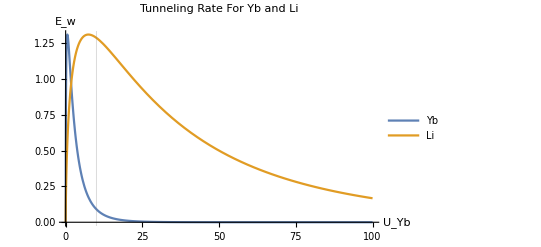

```mathematica
J[s_]:=(4/√π)s^(3/4)Exp[-2√s];
(*Plotting the tunneling rate. Note: this expression is valid only when s>10. First vertical line shows the lower boundary where Subscript[E, w,Yb] is valide; second line is for Subscript[E, w,Li]*)
Plot[{4J[Subscript[U, Yb]],4J[(2.2/29)Subscript[U, Yb]]},{Subscript[U, Yb],0,100},PlotRange->All,AxesLabel->{"U_Yb","E_w"},PlotLabel->"Tunneling Rate For Yb and Li", PlotLegends->{"Yb","Li"},GridLines->{{10, 290/2.2},{10,10}}]
```

```mathematica
notify[asc_]:=RunProcess[{"osascript","-e",StringTemplate["display notification \"`message`\" with title \"`title`\""][asc]}]
notify[<|"message"->"I'm finished!","title"->"Mathematica"|>]
```